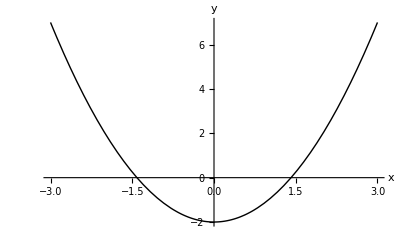

```mathematica
quad=Plot[x^2-2,{x,-3,3},PlotStyle->Black,AxesLabel->{x,y}]
```

```mathematica
Export["quad2Plot.pdf",quad]
```

quad2Plot.pdf

```mathematica
Export["cubicPlot.pdf",Plot[x^3-6x+1,{x,-3,3},PlotStyle->Black,AxesLabel->{x,y}]]
```

cubicPlot.pdf

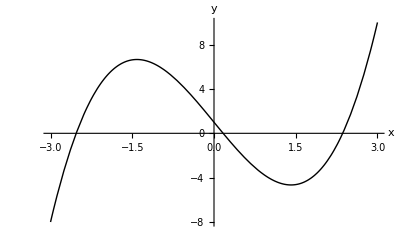

```mathematica
Plot[x^3-6x+1,{x,-3,3},PlotStyle->Black,AxesLabel->{x,y}]
```

```mathematica
u1=((-1 + Sqrt[-31])/(2))^(1/3)
v1=6/(3*u1)
N[u1+v1]
NSolve[x^3-6x+1==0,x]
```

(1/2 (-1+ⅈ √31))^(1/3)

2/(1/2 (-1+ⅈ √31))^(1/3)

2.36147-1.11022×10^-16 ⅈ

{{x→-2.52892},{x→0.167449},{x→2.36147}}

```mathematica
u2=((-1 - Sqrt[-31])/(2))^(1/3)
v2=6/(3*u)
N[u2+v2]
NSolve[x^3-6x+1==0,x]
```

(1/2 (-1-ⅈ √31))^(1/3)

2/(1/2 (-1-ⅈ √31))^(1/3)

2.36147+1.11022×10^-16 ⅈ

{{x→-2.52892},{x→0.167449},{x→2.36147}}

```mathematica
N[(2-Sqrt[5])^(1/3)-1/(2-Sqrt[5])^(1/3)]
```

-0.5+1.93649 ⅈ

```mathematica
NSolve[x^3+3x-4==0,x]
```

{{x→-0.5-1.93649 ⅈ},{x→-0.5+1.93649 ⅈ},{x→1.}}

```mathematica
u+v
```

2/(1/2 (-1-ⅈ √31))^(1/3)+(1/2 (-1-ⅈ √31))^(1/3)